## Yukawa potential

```mathematica
(* write down effective equation of motion, *)
```

```mathematica
V[r_]:=-k ⅇ^(-α r)/r;
effectivePot=l^2/(2 μ r^2)+V[r]
```

-(ⅇ^(-r α) k)/r+l^2/(2 r^2 μ)

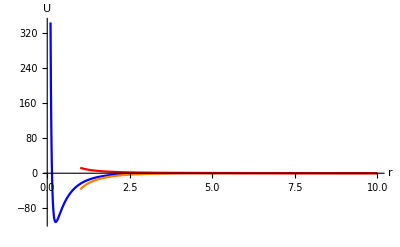

```mathematica
Show[Plot[effectivePot/.{k->100,μ->1,l->5,α->1}/.r->r1,{r1,0.1,10},AxesLabel->{r,U},PlotRange->All,PlotStyle->{Blue}],Plot[-k ⅇ^(-α r)/r/.{k->100,α->1}/.r->r1,{r1,1,10},AxesLabel->{r,U},PlotRange->All,PlotStyle->{Orange}],Plot[l^2/(2 r^2 μ)/.{k->100,μ->1,l->5}/.r->r1,{r1,1,10},AxesLabel->{r,U},PlotRange->All,PlotStyle->{Red}]]
```

```mathematica
Clear[V]
```

```mathematica
KeplersEqn=(Solve[D[(H==l^2/(2 μ r[t]^2)+V[r[t]]+1/2 μ r'[t]^2), t],r''[t]]//Expand//Flatten)/.Rule->Equal
```

{r''[t]==l^2/(μ^2 r[t]^3)-V'[r[t]]/μ}

```mathematica
r''[t]==l^2/(μ^2 r[t]^3)-V'[r[t]]/μ/.D[{V[r[t]]->-k ⅇ^(-α r[t])/r[t]}, r[t]]
```

r''[t]==-((ⅇ^(-α r[t]) k)/r[t]^2+(ⅇ^(-α r[t]) k α)/r[t])/μ+l^2/(μ^2 r[t]^3)

```mathematica
{v'[t]==-((ⅇ^(-α r[t]) k)/r[t]^2+(ⅇ^(-α r[t]) k α)/r[t])/μ+l^2/(μ^2 r[t]^3),r'[t]==v[t],l==μ  r[t]^2 θ'[t]}
```

{v'[t]==-((ⅇ^(-α r[t]) k)/r[t]^2+(ⅇ^(-α r[t]) k α)/r[t])/μ+l^2/(μ^2 r[t]^3),r'[t]==v[t],l==μ r[t]^2 θ'[t]}

```mathematica
solution1=NDSolve[{v'[t]==-((ⅇ^(-α r[t]) k)/r[t]^2+(ⅇ^(-α r[t]) k α)/r[t])/μ+l^2/(μ^2 r[t]^3),r'[t]==v[t],l==μ r[t]^2 θ'[t],r[0]==1,θ[0]==0,v[0]==(√(-l^2+2 H μ r[0]^2-2 μ r[0]^2 V[r[0]]))/(μ r[0])/.{r[0]->1,V[r_]->-k ⅇ^(-α r)/r,H->0}}/.{α->1,k->100,μ->1,l->5},{r[t],θ[t],v[t]},{t,0,30},MaxSteps->20000,Method->"Automatic",WorkingPrecision->20]//Flatten
```

{r[t]→InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t],θ[t]→InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t],v[t]→InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t]}

```mathematica
x=r[t] Cos[θ[t]]/.solution1
y=r[t] Sin[θ[t]]/.solution1
```

Cos[InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t]] InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t]

Sin[InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t]] InterpolatingFunction[{{0, 30.000000000000000000}}, <>][t]

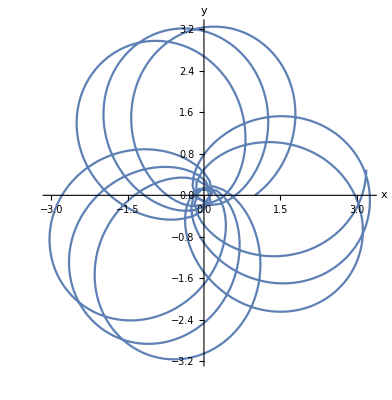

```mathematica
ParametricPlot[{x,y},{t,0,30},AxesLabel->{"x","y"},PlotRange->All]
```

```mathematica
Solve[H==l^2/(2 μ r[t]^2)+V[r[t]]+1/2 μ r'[t]^2,r'[t]]
```

{{r'[t]→-(√(-l^2+2 H μ r[t]^2-2 μ r[t]^2 V[r[t]]))/(μ r[t])},{r'[t]→(√(-l^2+2 H μ r[t]^2-2 μ r[t]^2 V[r[t]]))/(μ r[t])}}